```mathematica
AutomatasEquiv[n_,m_,k_]:=Module[{A=RandomAutomaton[n,m,0.5],B=RandomAutomaton[n,m,0.5]},
While[EquivalentAutomataQ[A,B]==False || LanguageSize[A,-k]==0,
A=RandomAutomaton[n,m,0.5];
B=RandomAutomaton[n,m,0.5];
];
Print[ShowAutomaton[A], "",ShowAutomaton[B]];
];
```

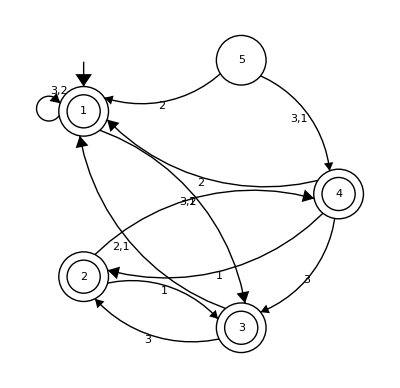
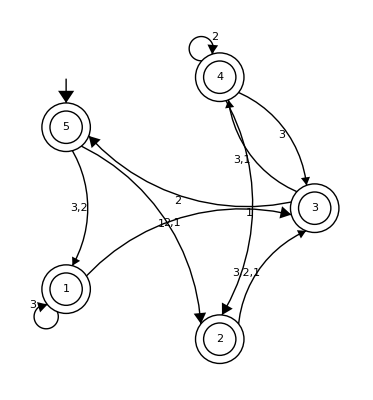

```mathematica
AutomatasEquiv[5,3,3]
```